```mathematica
GraphSolutions2[g_,pre_, circle_]:=Block[{sols, colors},
sols=ToVars2[g,pre];
colors=Map[Sort[ToColors[#]]&,sols];
colors=Map[Map[#[[1]]->If[MemberQ[circle,#[[1]]],Lighter[#[[2]]],Darker[#[[2]]]]&,#]&, colors];
colors=Map[Map[Last[#]&,#]&,colors];
colors
]
```

```mathematica
Take[deps2,3]
```

{{1,2,{2,1<->4,2<->3}},{2,3,{2,2<->4,3<->5}},{2,4,{2,2<->5,1<->4}}}

```mathematica
HeaderFor[g_,circle_]:=Block[{result},
result=Table[If[MemberQ[circle,k],Style[k,Red,Italic,Underlined],k],{k,Sort[VertexList[g]]}];
result
]
```

```mathematica
MyGrid[g_,l_, circle_]:=Labeled[TableForm[GraphSolutions2[g,"x1==1&&x2==2&&x3==3",circle],
TableSpacing->{0,0},
TableHeadings->{None, HeaderFor[g,If[EdgeQ[g,circle[[2]]<->circle[[4]]],{},{circle[[2]],circle[[4]]}]
]}], ToString[ChromaticPolynomial[g,4]/24]<>" - " <> l]
```

```mathematica
Table[
With[{rec=deps2[[k]]},
With[
{cycle={rec[[3,2,1]],rec[[3,3,1]],rec[[3,2,2]],rec[[3,3,2]]}},
MyGrid[ReadGrof[rec[[1]]],"g"<>ToString[{rec[[1]],rec[[3,2]]}],cycle]
]
],
{k,10,20}
]
```

{1 | 2 | 3 | 4 | 5 | 6 | 7
RGBColor[Rational[2, 3], 0, 0] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[2, 3], Rational[2, 3], 0] | RGBColor[1, 1, Rational[1, 3]]1 - g{5, 3 <-> 5},1 | 2 | 3 | 4 | 5 | 6 | 7
RGBColor[Rational[2, 3], 0, 0] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[2, 3], Rational[2, 3], 0]1 - g{5, 4 <-> 5},1 | 2 | 3 | 4 | 5 | 6 | 7
RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[0, Rational[2, 3], 0] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[2, 3], Rational[2, 3], 0]1 - g{5, 2 <-> 6},1 | 2 | 3 | 4 | 5 | 6 | 7
RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[2, 3], Rational[2, 3], 0]1 - g{5, 3 <-> 6},1 | 2 | 3 | 4 | 5 | 6 | 7
RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[0, 0, Rational[2, 3]] | RGBColor[0, Rational[2, 3], 0] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]]1 - g{5, 2 <-> 5},1 | 2 | 3 | 4 | 5 | 6 | 7
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[2, 3], Rational[2, 3], 0] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[2, 3], Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1]
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[2, 3], Rational[2, 3], 0] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[1, 1, Rational[1, 3]]
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[0, Rational[2, 3], 0] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1]4 - g{6, 1 <-> 5},1 | 2 | 3 | 4 | 5 | 6 | 7
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[0, 0, Rational[2, 3]]
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[2, 3], Rational[2, 3], 0] | RGBColor[0, 0, Rational[2, 3]]
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[2, 3], Rational[2, 3], 0]
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[0, 0, Rational[2, 3]]4 - g{6, 3 <-> 5},1 | 2 | 3 | 4 | 5 | 6 | 7
RGBColor[Rational[2, 3], 0, 0] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[0, 0, Rational[2, 3]]
RGBColor[Rational[2, 3], 0, 0] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[0, 0, Rational[2, 3]]
RGBColor[Rational[2, 3], 0, 0] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[2, 3], Rational[2, 3], 0]
RGBColor[Rational[2, 3], 0, 0] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[0, 0, Rational[2, 3]]4 - g{6, 3 <-> 4},1 | 2 | 3 | 4 | 5 | 6 | 7
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[0, 0, Rational[2, 3]] | RGBColor[Rational[2, 3], Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[0, 0, Rational[2, 3]] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[2, 3], Rational[2, 3], 0] | RGBColor[Rational[1, 3], 1, Rational[1, 3]]
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[0, 0, Rational[2, 3]] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[1, 1, Rational[1, 3]]
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[0, 0, Rational[2, 3]] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[2, 3], Rational[2, 3], 0] | RGBColor[1, 1, Rational[1, 3]]
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[0, 0, Rational[2, 3]] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[2, 3], Rational[2, 3], 0] | RGBColor[1, 1, Rational[1, 3]]5 - g{7, 1 <-> 5},1 | 2 | 3 | 4 | 5 | 6 | 7
RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[2, 3], Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[0, Rational[2, 3], 0]
RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[0, Rational[2, 3], 0]
RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[2, 3], Rational[2, 3], 0]
RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[2, 3], Rational[2, 3], 0]
RGBColor[Rational[2, 3], 0, 0] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[Rational[2, 3], Rational[2, 3], 0]5 - g{7, 2 <-> 6},1 | 2 | 3 | 4 | 5 | 6 | 7
RGBColor[1, Rational[1, 3], Rational[1, 3]] | RGBColor[Rational[1, 3], 1, Rational[1, 3]] | RGBColor[Rational[1, 3], Rational[1, 3], 1] | RGBColor[Rational[2, 3], 0, 0] | RGBColor[1, 1, Rational[1, 3]] | RGBColor[0, Rational[2, 3], 0] | RGBColor[Rational[2, 3], 0, 0]1 - g{8, 1 <-> 5}}

RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[1, 1, 0]

RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[1, 1, 0]RGBColor[0, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 0, 1]RGBColor[0, 0, 1]

RGBColor[1, 0, 0]RGBColor[0, 0, 1]RGBColor[0, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[1, 1, 0]

RGBColor[1, 0, 0]RGBColor[0, 0, 1]RGBColor[1, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[0, 1, 0]

RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[0, 1, 0]RGBColor[1, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 0, 1]RGBColor[0, 0, 1]

RGBColor[1, 0, 0]RGBColor[1, 1, 0]RGBColor[0, 0, 1]RGBColor[1, 1, 0]RGBColor[1, 0, 0]RGBColor[0, 1, 0]RGBColor[0, 1, 0]

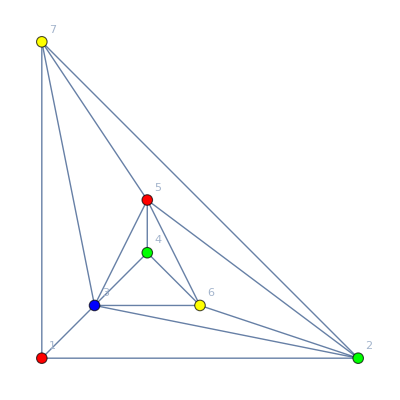
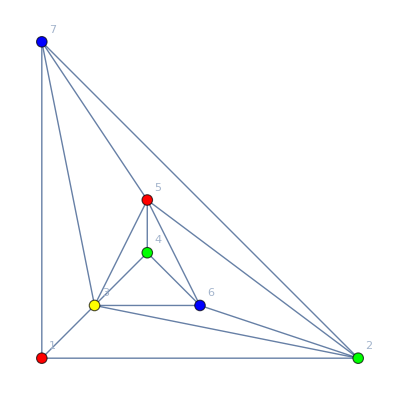
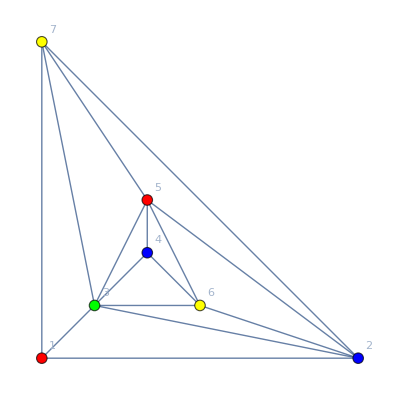
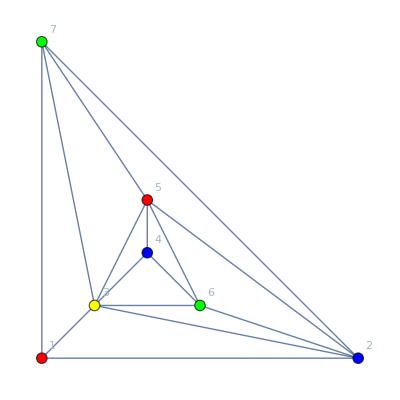
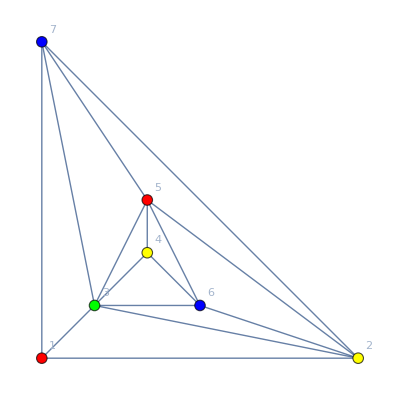
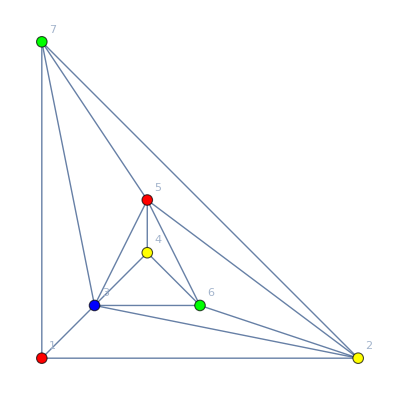

```mathematica
PaintGraph2[ReadGrof[5],"x1==1",VertexLabels->"Name"]
```

```mathematica
Table[
With[{rec=deps2[[k]]},
With[
{cycle={rec[[3,2,1]],rec[[3,3,1]],rec[[3,2,2]],rec[[3,3,2]]}},
MatrixForm[DistanceMatrix[ReadGrof[rec[[1]]]]]
]
],
{k,100,100}
]
```

{(0 | 1 | 1 | 1 | 1 | 1 | 2 | 2
1 | 0 | 1 | 2 | 1 | 2 | 1 | 2
1 | 1 | 0 | 1 | 2 | 1 | 1 | 1
1 | 2 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 2 | 1 | 0 | 2 | 1 | 2
1 | 2 | 1 | 1 | 2 | 0 | 2 | 2
2 | 1 | 1 | 1 | 1 | 2 | 0 | 1
2 | 2 | 1 | 1 | 2 | 2 | 1 | 0)}

```mathematica
Table[
With[{rec=deps2[[k]]},
With[
{g=ReadGrof[rec[[1]]]},
{rec,Length[Solve[ToLogical[g]&&Symbol["x"<>ToString[rec[[3,3,1]] ]]==Symbol["x"<>ToString[rec[[3,3,2]] ]],SymbolRange[g]]]}
]
],
{k,10,20}
]
```

{{{5,11,{2,3<->5,4<->7}},0},{{5,12,{2,4<->5,3<->6}},0},{{5,13,{2,2<->6,3<->5}},0},{{5,14,{2,3<->6,2<->4}},24},{{5,15,{2,2<->5,6<->7}},24},{{6,11,{2,1<->5,3<->7}},72},{{6,18,{2,3<->5,1<->4}},24},{{6,14,{2,3<->4,5<->6}},0},{{7,18,{2,1<->5,2<->7}},48},{{7,21,{2,2<->6,3<->5}},120},{{8,13,{2,1<->5,2<->3}},0}}